```mathematica
Clear["Global`*"]
$PlotTheme="Scientific";
```

```mathematica
PositivePart[x_]:=If[x>=0,x,0];
μ=1;
c=1;
R = {x, y, z};
$Assumptions = t∈Reals&x ∈ Reals && y ∈ Reals && z ∈ Reals && ρ ∈ Reals && ρ > 0 && θ ∈ Reals && ϕ ∈ Reals && k ∈ Reals && k > 0 && ω > 0&&c∈Reals&&c>0;
r = Sqrt[R . R];
predecessor[α_] := If[α == {0, 0, 0},
   {0, 0, 0},
   Select[
     Table[α - UnitVector[3, j], {j, 1, 3}],
     NonNegative@Min@# &,
     1
     ][[1]]
   ];
firstNonzeroDim[α_] := Position[
     α,
     _?(# > 0 &),
     Infinity, 1
     ][[1]][[1]];
ϵ=1/μ/c^2;
g[α_,f_,direction_] :=If[f===0,0,
If[α == {0, 0, 0},
   1/4/π/r f,
Block[{j, α1, ga},
α1 = α;
j = firstNonzeroDim[α];
α1[[j]] = α1[[j]] - 1;
ga = g[α1,f,direction];
D[ga, R[[j]]] -direction R[[j]]/r D[ga,t]/c//Expand
]
]
];
h[α_,f_,direction_] :=g[α,f,direction]
SimplifiedHeaviside[x_] := If[x >= 0, 1, 0];
SafeMoment[CurrentMoment_,α_,dim_]:=If[AllTrue[α,#>=0&],
CurrentMoment[α,dim],
0];
ChargeMoment[α_, CurrentMoment_, dim_,direction_] :=-direction  Sum[If[dim == j,
    α[[j]] SimplifiedHeaviside[α[[j]] - 2] (α[[j]] - 1) Integrate[SafeMoment[CurrentMoment,(α[[j]] - 2) UnitVector[3, j] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {j }]], j],t],
    α[[j]] α[[dim]] SimplifiedHeaviside[α[[j]] - 1] SimplifiedHeaviside[α[[dim]] - 1] Integrate[SafeMoment[CurrentMoment,(α[[j]] - 1) UnitVector[3, j] + (α[[dim]] - 1) UnitVector[3, dim] + Total[α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {dim, j}]], j],t]
    ],
   {j, 1, 3}]
ElectricMoment[α_, CurrentMoment_, dim_,direction_] := direction μ D[CurrentMoment[α, dim],t] + 1/ϵ ChargeMoment[α, CurrentMoment, dim,direction]
MagneticMoment[α_,CurrentMoment_, dim_,direction_] := -μ direction Sum[LeviCivitaTensor[3][[dim]][[i]][[j]] SimplifiedHeaviside[α[[i]] - 1] α[[i]] CurrentMoment[(α[[i]] - 1) UnitVector[3, i] +Total[ α[[#]] UnitVector[3, #] & /@ Complement[{1, 2, 3}, {i}]], j],
   {i, 1, 3}, {j, 1, 3}]
Field[α_, CurrentMoment_, MomentFunction_, dim_,direction_] :=(-1)^Norm[α, 1]/(Times @@ (Factorial/@ α)) h[α,MomentFunction[α, CurrentMoment, dim,direction],direction]
ElectricField[α_, CurrentMoment_, dim_,direction_] := Field[α, CurrentMoment, ElectricMoment, dim,direction];
MagneticField[α_, CurrentMoment_, dim_,direction_] := Field[α, CurrentMoment, MagneticMoment, dim,direction];
On[Assert]
CurrentMoment[α_, dim_] := If[α == {0, 0, 0} && dim == 3, p'[t], 0]
EfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", 
Table[
Sum[ElectricField[{ax, ay, az}, CurrentMoment, dim,-1],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}]ⅇ^(ⅉ k ρ)/.
∫p[t]ⅆt->1/ⅉ/ω p/.
p''[t]->-ω^2 p/.
p'[t]->ⅉ ω p/.
p[t]->p/.
ω->c k;
BfieldThis = Simplify@TransformedField["Cartesian" -> "Spherical", Table[Sum[MagneticField[{ax, ay, az}, CurrentMoment, dim,-1],
      {ax, 0, 2}, {ay, 0, 2 - ax}, {az, 0, 2 - ax - ay}],
     {dim, 1, 3}], R -> {ρ, θ, ϕ}]ⅇ^(ⅉ k ρ)/.
∫p[t]ⅆt->1/ⅉ/ω p/.
p''[t]->-ω^2 p/.
p'[t]->ⅉ ω p/.
p[t]->p/.
ω->c k;
P = {0, 0, p};
n = R/r;
HJackson = TransformedField["Cartesian" -> "Spherical",
    c k^2/4/π n×P Exp[ⅉ k r]/r (1 - 1/ⅉ/k/r),
    R -> {ρ, θ, ϕ}] // Simplify;
EJackson = TransformedField["Cartesian" -> "Spherical",
    1/4/π/ϵ Exp[ⅉ k r] (k^2/r (n×P)×n + (3 n (n . P) - P) (1/r^3 - ⅉ k/r^2)),
    R -> {ρ, θ, ϕ}] // Simplify;
Assert[Simplify[BfieldThis - HJackson μ] == {0, 0, 0}]
Assert[Simplify[EfieldThis - EJackson] == {0, 0, 0}]
Clear[CurrentMoment, EfieldThis, BfieldThis, P, n, HJackson, EJackson]
```

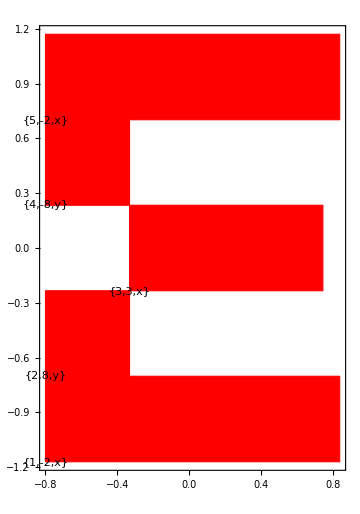

```mathematica
dirName=ToString@NotebookDirectory[];
a=4;
length=2a;
x1s={(*E*)0,0,10,0,0,(*P*)45,45,55,68,55,(*F*)91,91,101,91,(*L*)136,136};
x2s={(*E*)0,10,20,30,40,(*P*)0,20,20,30,40,(*F*)0,30,20,40,(*L*)10,0};
ws={(*E*)35,10,23,10,35,(*P*)10,10,23,10,23,(*F*)10,10,23,35,(*L*)10,35};
hs={(*E*)10,10,10,10,10,(*P*)20,30,10,10,10,(*F*)20,10,10,10,(*L*)40,10};
amplitudes={-2,8,6/2,-8,-2,(*P*)2,1,1,-1,2,(*F*)2,2,2,-2,(*L*)1,-1};
polarities={1,2,1,2,1,(*P*)2,2,1,2,1,(*F*)2,2,1,1,(*L*)2,1};
d1 = a;
lengthLogo = 171;

d1=a/5;
slice=;;5;
x1s=x1s[[slice]];
x2s=x2s[[slice]];
ws=ws[[slice]];
hs=hs[[slice]];
amplitudes=amplitudes[[slice]];
polarities=polarities[[slice]];

d2 = a * 50 / lengthLogo;
Graphics[Flatten@
MapThread[
{{EdgeForm[Thin],Red,Rectangle[{#1,#2},{#1+#3,#2+#4}]},
{Black,Text[{#5,#6,{x,y}[[#7]]},{#1,#2}]}
}&
,{x1s/lengthLogo length-d1,x2s/lengthLogo length-d2,ws/lengthLogo length,hs/lengthLogo length,Range[Length@x1s],amplitudes,polarities}],
ImageSize->Medium,
Frame->True
]
IntJ=Function[{x0,σ,m},
1/(m+1)((x0+σ/2)^(m+1)-(x0-σ/2)^(m+1))
];
CJ=Function[{α,x1,x2,w,h},
IntJ[x1+w/2,w,α[[1]]]IntJ[x2+h/2,h,α[[2]]]
];
CurrentMoment=If[#1[[3]]==0,
Exp[-t^2]Sum[
If[polarities[[i]]==#2,
CJ[#1,x1s[[i]]/lengthLogo length-d1,x2s[[i]]/lengthLogo length-d2,ws[[i]]/lengthLogo length,hs[[i]]/lengthLogo length]amplitudes[[i]],
0],
{i,1,Length@x1s}],
0]&;
```

```mathematica
Efield=0;
```

```mathematica
Efield=Import[dirName<>"/data/field-order-61-a-4.mx"];
```

```mathematica
d=Table[
Monitor[
Efield+=#1+#2&@@ParallelTable[
Table[
Sum[
ElectricField[{ax,order-ax,0},CurrentMoment,dim,direction]/.t->0-direction r/.z->0,
{ax,0,order}],
{dim,1,2}
],{direction,-1,1,2}
];
Export[dirName<>"/data/field-order-"<>ToString[order]<>"-a-"<>ToString[a]<>".mx",
Efield],
order]//AbsoluteTiming,
{order,62,71}
]
```

{{0.040693,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-0-a-4.mx},{0.03231,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-1-a-4.mx},{0.038181,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-2-a-4.mx},{0.055669,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-3-a-4.mx},{0.099852,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-4-a-4.mx},{0.158555,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-5-a-4.mx},{0.257034,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-6-a-4.mx},{0.44195,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-7-a-4.mx},{0.704318,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-8-a-4.mx},{1.25376,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-9-a-4.mx},{1.90494,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-10-a-4.mx},{3.39027,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-11-a-4.mx},{4.83476,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/field-order-12-a-4.mx}}

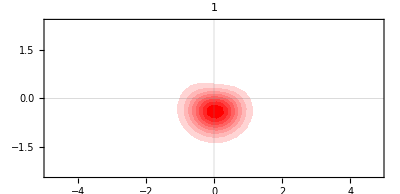
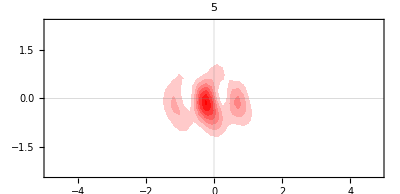
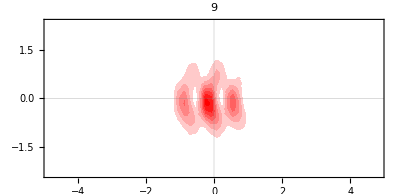
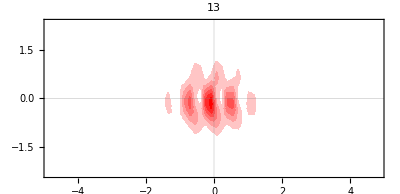
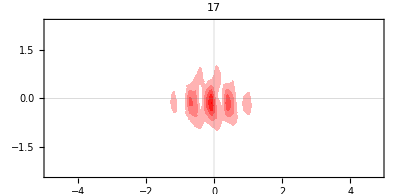
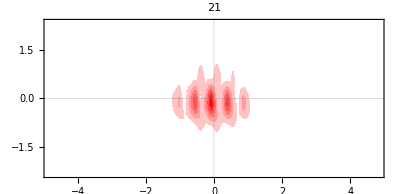
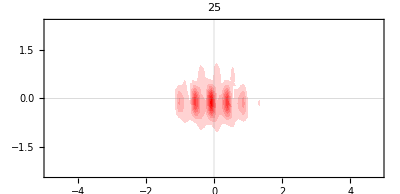
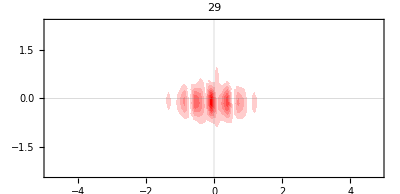

```mathematica
Table[
Monitor[
Block[{imported,x,y,z},
imported=Import[ToString@NotebookDirectory[]<>"data/order-"<>ToString[order]<>"-a-4.mx"];
x=imported["x"];
y=imported["y"];
z=imported["discrete norm"];
ListContourPlot[
Flatten[
Table[
{x[[i]],y[[j]],z[[i,j]]},
{i,1,Length@x},{j,1,Length@y}],1],
PlotRange->Full,
PlotLabel->order,
AspectRatio->Max@y/Max@x,
ColorFunction->(Blend[{White,Red},#1]&),
ContourStyle->None
]
],order],
{order,1,57,4}
]
```

-0.000139722+0.000148093 x-0.00003922 x^2+3.35577×10^-6 x^3

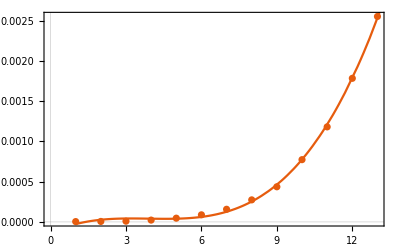

0.373358

```mathematica
d=dSingle[[;;,1]];
d=Table[{i,d[[i]]/3600},{i,1,Length[d]}];
fitted=Fit[
d,
{1,x,x^2,x^3},x
]
Show[
ListPlot[d],
Plot[fitted,{x,1,51}]
]
fitted/.x->52
```

```mathematica
Table[Monitor[
Efield=Import[ToString@NotebookDirectory[]<>"data/field-order-"<>ToString[order]<>"-a-"<>ToString[a]<>".mx"];
norm=Total[Efield^2];
plotLimitX=6/5a;
plotLimitY=2a 50/171;
nPointsX=61;
nPointsY=Round[nPointsX plotLimitY/plotLimitX];
xd=Subdivide[-plotLimitX,plotLimitX,nPointsX];
yd=Subdivide[-plotLimitY,plotLimitY,nPointsY];
normd=ParallelTable[
N[norm/.x->xd[[i]]/.y->yd[[j]],100],
{i,1,Length@xd},{j,1,Length@yd}];
Export[ToString@NotebookDirectory[]<>"/data/order-"<>ToString[order]<>"-a-"<>ToString[a]<>".mx",
<|"x"->xd,"y"->yd,"discrete norm"->normd|>],
order],{order,1,9,2}]
```

{/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/order-1-a-4.mx,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/order-3-a-4.mx,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/order-5-a-4.mx,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/order-7-a-4.mx,/Users/elias/Dropbox/Documents/EPFL/Doctorat/etr/papers/pynoza/funknoza//data/order-9-a-4.mx}